# Arm state visualization

## Import

```mathematica
(*ClearAll["Global`*"]
Clear["Global`*"]*)

AppendTo[$Path,"/Users/thomasbuhrmann/Library/Mathematica/Packages/LevelScheme"];
Get["LevelScheme`"];

(* Best *)
dirNameB1 = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_01_16__12_26_42"; (* Mv1234 0.994 *)
dirNameB2 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_04__17_49_45"; (* Mv1234 0.992 *)
dirNameB3 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_30__13_57_40"; (* Mv24 0.9918 *)
dirNameB4 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_27__21_30_56"; (* Mv1234 0.9928 *)
dirNameB5 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_19__21_52_30"; (* Mv1234 0.9918 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_03_21__13_38_43"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_11__17_43_03"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_25__14_55_44"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_26__15_44_55"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_27__00_48_28"; (* *)

(* Ablation *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__11_19_24"; (* Best: Inc from 13_04_27__13_03_45: 0.9897 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__14_01_20"; (* Like above, but without IbInterseg: 0.984 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__19_52_19"; (* Like above, but without IbIaExc: 0.975 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_23__10_26_30"; (* Like above, but no Ib at all: 0.970 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55"; (* No interneurons at all, but GO sig *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10"; (* No interneurons at all: 0.946 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_09__20_37_11"; (* Mv123456 Run from _19_47_32 *)

(* Dirs 8M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__02_07_37"; (* 8M: 0.95. Soso.*)

(* Dirs 6M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__19_15_19"; (* 6M_1: 0.967. Two moves bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_16__10_04_00"; (* 6M_1 inc: 0.9723. Still two bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_17__14_13_56"; (* 6M_1 inc2: 0.987. Pretty good. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__11_25_57/"; (* 6M_2: 0.967. Two moves bad again. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__13_22_34/"; (* 6M_2: 0.9685. Two moves bad again. *)


(* Dirs 4M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_31"; (* 4M diag: 0.9916*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_29"; (* 4M diag: 0.9914 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Dirs/0/13_07_08__16_18_21/"; (* 4M straight, slow: 0.991. Wobbly. *)
(* Mv1234 check whether 4M net works for 1234: 0.96011, 0.946. No! *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10/"; 

(* Energy min *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_18__18_39_18/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__09_46_01/"; (* network: 1.98171 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__10_56_15/"; (* network asymsp: 1.98431 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__11_40_37/";(* network symsp noVelRef: 1.98415 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__14_11_55/";(* R1 network symsp noVelRef: 1.9839 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__10_06_33/"; (* Engy min PD: 1.982 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_26_06/"; (* Engy min PD noVelRef: 0.993 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_33_04/"; (* Engy min PD noVelRef dbgain: 0.9934 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_46_28/"; (* Engy min PD noVelRef higher gain: 0.994 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_52_51/"; 
(* Engy min PD noVelRef higher gain, exp:  *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_19__20_45_29/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_23__17_33_44"; 



(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_02_06__22_44_11";*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_21__15_16_27"; (* Mv1234 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_17__17_18_17"; (* Mv1234 *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_19__19_38_08"; (* Mv34 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_18__14_18_53"; (* Mv12 Ext OL *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_17__15_14_34"; (* Mv12 Norm OL *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_16__17_44_26"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_06_10__02_25_24"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_12__19_20_02/"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_13__13_03_05/"; (* Mv1 *)*)

figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";
SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]];
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
font="Arial";
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.53 (January 10, 2013)
View color paletteVisit home page  -Graphics-

3601

## Fitness

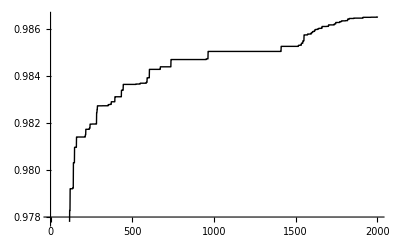

0.986514

```mathematica
fitP =ListLinePlot[fitness[[1;;Length[fitness]]],PlotStyle->Black,PlotRange->Automatic,ImageSize->400]
maxFit = Max[fitness]
```

## Robustness

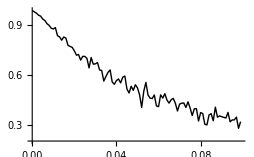

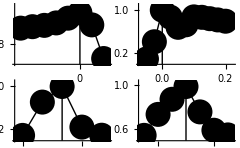

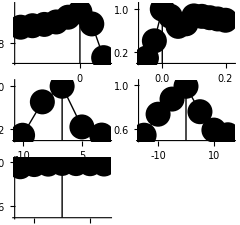

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/generalisation.eps

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/readaptConstVel.eps

```mathematica
(* Mutations *)
SetDirectory["/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__19_27_46"];
mutFitData=Import["Fitness.txt", "Table"];
fitData = mutFitData[[2;;-2]];
mutFit =fitData[[;;,1]];
grouped = Partition[mutFit,100];
means=Mean[Transpose[grouped]];
Length[means];
x=Range[0,0.099,0.001];
Length[x];
cm=72/2.54;
robPl=ListLinePlot[Transpose[{x,means}],PlotStyle->Black,AxesOrigin->{0,0.2},ImageSize->9cm]
(*Export[figExpPath<>"robustness.svg",robPl]*)

(* Shifts *)
(*opts={PlotMarkers->None,PlotStyle->Black,FillingStyle->{Black,AbsoluteThickness[10]},Filling->Axis,BaseStyle->{FontFamily->font}};*)
opts={PlotStyle->Black,BaseStyle->{FontFamily->font},Mesh->All,MeshStyle->{PointSize[0.045],Black},BaseStyle->{FontFamily->font}};
SetOptions[LinTicks,MajorTickLength->{0.03,0},MinorTickLength->{0.01,0},ShowMinorTicks->False];

shiftFit={0.896, 0.905,0.913,0.928,0.957,0.9896,0.916,0.71};
x=Range[-25,10,5];
shiftPl=ListLinePlot[Transpose[{x,shiftFit}],AxesOrigin->{-27.5,0.95*Min[shiftFit]},PlotRange->{{-27.5,12.5},{0.95*Min[shiftFit],1.05*Max[shiftFit]}},opts,
Ticks->{LinTicks[-30,10],LinTicks[0.5,1]}, 
Epilog->{Line[{{0,0.95*Min[shiftFit]},{0,Max[shiftFit]}}]}];
shiftPl = Show[shiftPl];

(* Durations *)
durFits = {0.088,0.406,0.9896,0.8607,0.6723,0.719,0.865,0.857,0.832,0.809,0.785};
x=Range[-0.05,0.2,0.025];
durPl=ListLinePlot[Transpose[{x,durFits}],AxesOrigin->{-0.075,Min[durFits]-0.1*Max[durFits]},PlotRange->{{-0.075,0.225},{Min[durFits]-0.1*Max[durFits],1.1*Max[durFits]}},opts,
Ticks->{LinTicks[-0.05,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[durFits]-0.1*Max[durFits]},{0,Max[durFits]}}]}];

(* Amplitudes *)
ampFits = {0.0818,0.7,0.9896,0.2356,0.085};
x=Range[-10,10,5];
ampPl=ListLinePlot[Transpose[{x,ampFits}],AxesOrigin->{-12,Min[ampFits]-0.1*Max[ampFits]},PlotRange->{{-12,12},{Min[ampFits]-0.1*Max[ampFits],1.1*Max[ampFits]}},opts,
Ticks->{LinTicks[-10,10],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[ampFits]-0.1*Max[ampFits]},{0,Max[ampFits]}}]}];

(* Const velocity (changing duration and amplitude in proportion) *)
velFits = {0.54, 0.733,0.872,0.9896,0.756,0.587,0.544};
x=Range[-15,15,5];
velPl=ListLinePlot[Transpose[{x,velFits}],AxesOrigin->{-17,Min[velFits]-0.05*Max[velFits]},PlotRange->{{-17,17},{Min[velFits]-0.05*Max[velFits],1.05*Max[velFits]}},opts,
Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.5,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[velFits]-0.05*Max[velFits]},{0,Max[velFits]}}]}];

(* Readapted Const velocity (changing duration and amplitude in proportion) *)
revelFits = {0.959, 0.979,0.983,0.9896,0.988,0.987,0.984};
x=Range[-15,15,5];
revelPl=ListLinePlot[Transpose[{x,revelFits}],AxesOrigin->{-17,Min[velFits]-0.05*Max[velFits]},PlotRange->{{-17,17},{Min[velFits]-0.05*Max[velFits],1.05*Max[velFits]}},opts,Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.5,1,TickLabelStep->2,TickLabelStart->1]},
Epilog->{Line[{{0,Min[velFits]-0.05*Max[revelFits]},{0,Max[revelFits]}}]} ];

general=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl}}], ImageSize->8.5cm]
readapt=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl},{revelPl}}], ImageSize->8.5cm]
(*readapt = Show[revelPl, ImageSize->8.5cm]*)

Export[figExpPath<>"generalisation.eps",general]
Export[figExpPath<>"readaptConstVel.eps",readapt]

SetDirectory[dirName];
```

## Config

```mathematica
dt = 0.001;
leadIn = 0.1;
leadOut = 0.2;
moveDuration = 0.3;
bestFitDelay = -0.0 / dt;
(*plotDuration = (moveDuration+leadOut/3) / dt;*)

trialDuration = leadIn+moveDuration+leadOut;
frontLead =0.1;
backLead = 1.0*leadOut;

numData/(trialDuration/dt)
Round[numData/(trialDuration/dt)]
numTrials=Round[numData/(trialDuration/dt)]

SetTrial[trial_]:=Module[{},
t0=2 +((leadIn-frontLead+ (trial*trialDuration))/dt);
tn=-2 +t0+(leadIn + moveDuration+backLead)/dt;
time=Range[tn-t0]*dt;
];

SetTrial[0];

padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, PlotRange->All, ImagePadding->padds};
graphicsWidth = 600;
font="Arial";
SetOptions[Plot,BaseStyle->{FontFamily->font}];
pad={{20,10},{15,10}};
```

6.00167

6

6

## Functions

```mathematica
NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_, delay_:0]:=Table[data[[i,NtoI[name]]],{i,t0+delay,tn-1+delay}];
TimePlot[name_, options_, delay_:0,Scale_:1] := ListLinePlot[Transpose[{time,Scale*NtoD[name, delay]}], Join[options,plotOptions]];
TimePlotD[data_, options_, Scale_:1] := ListLinePlot[Transpose[{time,Scale*data}], Join[plotOptions,options]];

Maxima[x_,time_]:=Module[{max,peaks, times},
max = 1+Position[Differences[Sign[Differences[x]]],-2];
peaks = Extract[x, max];
times = Extract[time,max];
maxima = Transpose[{Flatten[times],peaks}];
maxima
]

Minima[x_,time_]:=Module[{min,peaks, times},
min = 1+Position[Differences[Sign[Differences[-x]]],-2];
peaks = -Extract[-x, min];
times = Extract[time,min];
minima = Transpose[{Flatten[times],peaks}];
minima
]

TimePlotMaxima[x_,time_, opt_:{}]:= ListPlot[Maxima[x,time],opt]
TimePlotMinima[x_,time_,opt_:{}]:= ListPlot[Minima[x,time],opt]
TimePlotOptima[x_, time_, opt1_:{},opt2_:{}]:=Module[{ma,mi},
ma=TimePlotMaxima[x, time,Join[{PlotStyle->Black},opt1]];
mi=TimePlotMinima[x,time,Join[{PlotStyle->Red},opt2]];
mami=Show[ma, mi];
mami
]

Shift[list_,del_]:=Module[{},
res=Drop[list,del];
res = If[del<0,
PadLeft[res,Length[list],res[[1]]],
PadRight[res,Length[list],res[[Length[res]]]]
]
];

(*l=Range[0,10]
l4=Shift[l,-2]*)
```

## All trajectories

28.3465

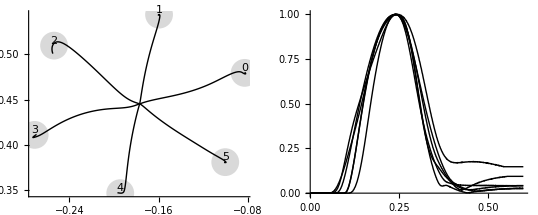

```mathematica
PlotTraj[trial_]:=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
elbX=NtoD["elbX"];
elbY=NtoD["elbY"];
desX=NtoD["desX"];
desY=NtoD["desY"];
positions=Transpose[{x,y}];
elbPositions=Transpose[{elbX,elbY}];
desPositions=Transpose[{desX,desY}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->{Black},AxesOrigin->{Min[x],Min[y]}];
pos0=First[positions];
elb0=First[elbPositions];
posN=Last[positions];
elbN=Last[elbPositions];
startPos = Graphics[{PointSize[Large],Point[pos0]}];
elbStartPos = Graphics[{LightGray,PointSize[Large],Point[elb0]}];
desEndPos=Graphics[{LightGray,PointSize[0.05],Point[Last[desPositions]]}];
label=Graphics[Text[trial,Last[desPositions],{0,-2}]];
lower0=Graphics[{LightGray,Line[{elb0, pos0}]}];
upper0=Graphics[{LightGray,Line[{{0,0}, elb0}]}];
lowerN=Graphics[{LightGray,Line[{elbN, posN}]}];
upperN=Graphics[{LightGray,Line[{{0,0}, elbN}]}];
optimal = Graphics[{LightGray,Dashed,Line[{pos0, Last[desPositions]}]}];
Show[(*elbStartPos,lower0,upper0,*)(*lowerN,upperN, optimal,*) (*startPos,*)desEndPos,cartesianPos,label,BaseStyle->{FontFamily->font}]
]

TangVels[trial_] :=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]]
]

MaxTangVelPos[trial_]:=Module[{}, tangVels = TangVels[trial];Position[tangVels,Max[tangVels]][[1]] ]
maxVelPos = Flatten[Map[MaxTangVelPos,Range[0,numTrials-1,1]]];
velOff = maxVelPos-Min[maxVelPos];

PlotTangVels[trial_]:=Module[{},
vels=TangVels[trial];
(* Shift so peaks coincide *)
vels = Drop[vels,velOff[[trial+1]]];
vels=PadRight[vels,Length[vels]+velOff[[trial+1]], Last[vels]];
(* Scale to same peak *)
maxVel =Max[Map[Norm,vels]];
vels = vels / maxVel;
col = Black;(*If[trial < 2,Black,Gray];*)
ln = {};(*If[EvenQ[trial],{},Dashed];*)
tangVel=TimePlotD[vels,{PlotStyle->{col, ln},BaseStyle->{FontFamily->font}}]
];

PlotAngles[trial_,mmin_:50,mmax_:100]:=Module[{},
SetTrial[trial];
shdAng=NtoD["angleShoulder"]/Degree;
shdAngDes=NtoD["desShoulder"]/Degree;
shdAngCom =NtoD["comShoulder"]/Degree;
elbAng=NtoD["angleElbow"]/Degree;
elbAngDes=NtoD["desElbow"]/Degree;
elbAngCom =NtoD["comElbow"]/Degree;
min=Min[Min[elbAng],Min[shdAng]]*0.9;
max=Max[Max[elbAng],Max[shdAng]]*1.1;
shdPl= TimePlotD[shdAng,{PlotStyle->{Black}}];
shdPlDes= TimePlotD[shdAngDes,{PlotStyle->{LightGray,Thick}}];
shdPlCom= TimePlotD[shdAngCom,{PlotStyle->{Black,Dashed}}];
elbPl= TimePlotD[elbAng,{PlotStyle->{Black}}];
elbPlDes= TimePlotD[elbAngDes,{PlotStyle->{LightGray,Thick}}];
elbPlCom= TimePlotD[elbAngCom,{PlotStyle->{Black,Dashed}}];
Show[elbPlDes, shdPlDes,shdPl,elbPl,shdPlCom,elbPlCom,PlotRange->{{0,0.6},{min,max}},AxesOrigin->{0,min},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[mmin,mmax,TickLabelStep->2,TickLabelStart->1]} ]
];

PlotAngVels[trial_]:=Module[{},
SetTrial[trial];
shdVel=NtoD["velocityShoulder"]/Degree;
elbVel=NtoD["velocityElbow"]/Degree;
shdPl= TimePlotD[shdVel,{PlotStyle->{Black}}];
elbPl= TimePlotD[elbVel,{PlotStyle->{Black,Dashed}}];
Show[elbPl, shdPl]
];

(* Forces applied at joints, total is more or less acceleration *)
PlotTrqsElb[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msD = NtoD["torqueElbow"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}}];
trq= TimePlotD[msD,{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin = 1.1*Min[{Min[itD],Min[msD],Min[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,Automatic}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0]} ]
]

PlotAMNElb[trial_]:=Module[{},
SetTrial[trial];
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ]
]

PlotAMNShd[trial_]:=Module[{},
SetTrial[trial];
aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ]
]

PlotTrqMElb[trial_]:=Module[{},
SetTrial[trial];
elbAgTrq = NtoD["ElbowFlexorTorque"];
elbAnTrq = NtoD["ElbowExtensorTorque"];
elbNetTrq = elbAgTrq - elbAnTrq;
max = Max[Max[Abs[elbAgTrq]],Max[Abs[elbAnTrq]],Max[Abs[elbNetTrq]]];
elbAgTorqueP = TimePlotD[elbAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbAnTorqueP = TimePlotD[elbAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
elbNetTrqP = TimePlotD[elbNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbTrq = Show[elbNetTrqP,elbAgTorqueP,elbAnTorqueP, PlotRange->{Automatic,{-max, max}}]
]

PlotTrqMShd[trial_]:=Module[{},
SetTrial[trial];
shdAgTrq = NtoD["ShoulderFlexorTorque"];
shdAnTrq = NtoD["ShoulderExtensorTorque"];
shdNetTrq = shdAgTrq - shdAnTrq;
max = Max[Max[Abs[shdAgTrq]],Max[Abs[shdAnTrq]],Max[Abs[shdNetTrq]]];
shdAgTorqueP = TimePlotD[shdAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}},ImageSize->2cm}];
shdAnTorqueP = TimePlotD[shdAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
shdNetTrqP = TimePlotD[shdNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
shdTrq = Show[shdNetTrqP,shdAgTorqueP,shdAnTorqueP,PlotRange->{Automatic,{-max, max}}]
]

PlotTrqsShd[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
msD = NtoD["torqueShoulder"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},ImageSize->22cm}];
trq= TimePlot["torqueShoulder",{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin =1.1* Min[{Min[itD],Min[msD],Min[totalD]}];
mmax =1.1* Max[{Max[itD],Max[msD],Max[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,mmax}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0,ShowMinorTicks->False]}]
]

trajsPl = Show[Table[PlotTraj[i],{i,0,numTrials-1}], Axes->True,AxesOrigin->{-0.45,0.25},ImagePadding->pad,AxesStyle->Thickness[.002]];


tangVelsPl=Show[Table[PlotTangVels[i],{i,0,numTrials-1}](*AspectRatio->1,*), ImagePadding->pad,AxesStyle->Thickness[.002]];

cm=72/2.54
angAndVel=Show[GraphicsRow[{trajsPl, tangVelsPl}],ImageSize->19cm]

(*Export[figExpPath<>"c1TrajAndVelNoIbIs.eps",angAndVel]*)

(*GraphicsGrid[Partition[Table[PlotAngles[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotAngVels[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotTrqsElb[i],{i,0,numTrials-1}],2],ImageSize->600]*)
tr1=0;
tr2=1;

(*mv12=GraphicsGrid[{{PlotAngles[tr1,40,90],PlotAngles[tr2,40,90]},{PlotTrqsElb[tr1,-2,2], PlotTrqsElb[tr2,-2,1]},{PlotTrqsShd[tr1,-12,12], PlotTrqsShd[tr2,-7,7]}},ImageSize->19cm,AxesStyle->Thickness[.002]]

mn12=GraphicsGrid[{{PlotAMNElb[tr1],PlotAMNShd[tr1],PlotAMNElb[tr2],PlotAMNShd[tr2]},
{PlotTrqMElb[tr1],PlotTrqMShd[tr1],PlotTrqMElb[tr2],PlotTrqMShd[tr2]}},ImageSize->22cm,AxesStyle->Thickness[.002]]

tr1=2;
tr2=3;
mv34=GraphicsGrid[{{PlotAngles[tr1],PlotAngles[tr2]},{PlotTrqsElb[tr1], PlotTrqsElb[tr2]},{PlotTrqsShd[tr1], PlotTrqsShd[tr2]}},ImageSize->19cm]


Export[figExpPath<>"c1AngleAndTorquesMv12.eps",mv12]
(*Export[figExpPath<>"c1AngleAndTorquesMv34.svg",mv34]
Export[figExpPath<>"aMN-Trq.pdf",mn12]*)
*)
```

```mathematica
TrajErr[trial_,del_:0] := Module[{},
SetTrial[trial];
(*Only actual movement, without leanIn or leadOut *)
tt0 = IntegerPart[leadIn/(2*dt)];
tt1 = -IntegerPart[leadOut/(2*dt)];
x = NtoD["x"][[tt0;;tt1]];
y = NtoD["y"][[tt0;;tt1]];
desX = Shift[NtoD["desX"][[tt0;;tt1]],del];
desY = Shift[NtoD["desY"][[tt0;;tt1]],del];
(*desX=NtoD["desX"][[tt0+del;;tt1+del]];*)
(*desY=NtoD["desY"][[tt0+del;;tt1+del]];*)
positions = Transpose[{x, y}];
desPositions = Transpose[{desX, desY}]; 
d=EuclideanDistance[desPositions[[1]],desPositions[[Length[desPositions]]] ];
se=MapThread[EuclideanDistance, {positions, desPositions}];
mse=Mean[se]*1000
];

maxShift=50;
TrajErrLag[trial_] := Module[{},
errs=Table[TrajErr[trial,d],{d,-maxShift,maxShift}];
Print[errs];
minErr=Min[errs];
minPos = Position[errs,minErr];
Print[-maxShift+minPos-1];
minErr
];

MaxRotVel[trial_] := Module[{},
SetTrial[trial];
elbVel = NtoD["velocityElbow"]/Degree;
shdVel = NtoD["velocityShoulder"]/Degree;
res = {Max[Abs[elbVel]], Max[Abs[shdVel]]}
]

(*t1=Table[TrajErr[i,0],{i,0,numTrials-1}]*)
t1l=Table[TrajErrLag[i],{i,0,numTrials-1}]
Mean[t1l]
t2=Table[Max[TangVels[i]],{i,0,numTrials-1}]
t3=Table[MaxRotVel[i],{i,0,numTrials-1}]
```

{7.71588,7.50083,7.28632,7.07247,6.85947,6.64771,6.437,6.2272,6.01824,5.8101,5.60277,5.39626,5.19058,4.98577,4.78185,4.57887,4.3769,4.176,3.97626,3.77779,3.58072,3.38522,3.19148,2.99977,2.81043,2.6239,2.44079,2.26194,2.08862,1.92274,1.76743,1.62812,1.51573,1.45301,1.42905,1.4355,1.46988,1.53233,1.62822,1.78034,1.96594,2.16222,2.36408,2.56964,2.77789,2.98819,3.20011,3.41333,3.62763,3.84283,4.05879,4.27539,4.49256,4.71021,4.92829,5.14674,5.36553,5.58461,5.80395,6.02354,6.24333,6.46332,6.68349,6.90382,7.12429,7.34489,7.56561,7.78644,8.00738,8.22841,8.44953,8.67072,8.89199,9.11332,9.33472,9.55617,9.77768,9.99924,10.2208,10.4425,10.6642,10.8859,11.1076,11.3294,11.5512,11.7731,11.9949,12.2168,12.4387,12.6607,12.8826,13.1046,13.3266,13.5486,13.7706,13.9926,14.2146,14.4367,14.6587,14.8808,15.1028}

{{-16}}

{11.3096,11.0896,10.8695,10.6494,10.4293,10.2092,9.98897,9.76875,9.5485,9.32822,9.10792,8.88758,8.66722,8.44683,8.22642,8.00598,7.78553,7.56505,7.34456,7.12405,6.90354,6.68302,6.4625,6.24198,6.02148,5.80099,5.58052,5.3601,5.13972,4.9194,4.69917,4.47903,4.25906,4.03922,3.81955,3.60006,3.38078,3.1618,2.94346,2.72614,2.51037,2.29687,2.08655,1.88063,1.6807,1.48899,1.30863,1.14428,1.00304,0.895987,0.8388,0.845679,0.918387,1.04294,1.19657,1.36992,1.55717,1.75407,1.95761,2.16573,2.37705,2.59067,2.80598,3.02255,3.24009,3.45839,3.67729,3.89667,4.11645,4.33656,4.55694,4.77755,4.99836,5.21933,5.44044,5.66168,5.88302,6.10445,6.32597,6.54755,6.7692,6.99091,7.21266,7.43446,7.6563,7.87817,8.10007,8.32201,8.54396,8.76594,8.98794,9.20996,9.43199,9.65404,9.8761,10.0982,10.3203,10.5424,10.7645,10.9866,11.2087}

{{0}}

{4.46118,4.32626,4.19791,4.07679,3.96361,3.85919,3.76437,3.68009,3.60736,3.54731,3.50118,3.47051,3.45728,3.46459,3.50037,3.56325,3.64478,3.74132,3.85049,3.97052,4.10005,4.238,4.38348,4.53576,4.69423,4.85839,5.0278,5.2021,5.38096,5.56412,5.75131,5.94229,6.13683,6.33468,6.53559,6.73926,6.94537,7.15361,7.36363,7.57514,7.78785,8.00155,8.21607,8.43127,8.64706,8.86336,9.08012,9.29728,9.51482,9.73268,9.95085,10.1693,10.388,10.6069,10.8261,11.0454,11.2649,11.4846,11.7045,11.9245,12.1446,12.3649,12.5852,12.8057,13.0263,13.247,13.4677,13.6886,13.9095,14.1305,14.3516,14.5727,14.7939,15.0151,15.2364,15.4578,15.6792,15.9006,16.1221,16.3436,16.5652,16.7868,17.0084,17.2301,17.4518,17.6735,17.8952,18.117,18.3388,18.5606,18.7824,19.0043,19.2261,19.448,19.6699,19.8918,20.1138,20.3357,20.5577,20.7796,21.0016}

{{-38}}

{7.00339,6.79638,6.59039,6.38552,6.18191,5.9797,5.77906,5.5802,5.38336,5.1888,4.99685,4.8079,4.62242,4.44096,4.2642,4.09295,3.92824,3.77132,3.62381,3.48783,3.36652,3.26657,3.19074,3.13272,3.09014,3.0616,3.04614,3.04302,3.05167,3.07163,3.10251,3.14405,3.19603,3.25832,3.33089,3.4138,3.5073,3.61183,3.72829,3.85888,4.00907,4.1768,4.36332,4.559,4.75891,4.96157,5.16632,5.37278,5.58069,5.78985,6.00009,6.21129,6.42334,6.63615,6.84963,7.06372,7.27836,7.49349,7.70908,7.92508,8.14146,8.35818,8.57522,8.79255,9.01014,9.22799,9.44607,9.66436,9.88285,10.1015,10.3204,10.5394,10.7585,10.9779,11.1973,11.4169,11.6365,11.8563,12.0762,12.2962,12.5163,12.7365,12.9567,13.1771,13.3975,13.618,13.8385,14.0592,14.2798,14.5006,14.7214,14.9422,15.1631,15.3841,15.6051,15.8262,16.0473,16.2684,16.4896,16.7108,16.932}

{{-23}}

{10.6615,10.4488,10.2364,10.0241,9.81197,9.60006,9.38836,9.17687,8.9656,8.75456,8.54375,8.33319,8.12289,7.91286,7.70312,7.49367,7.28454,7.07575,6.86731,6.65924,6.45157,6.24432,6.03752,5.8312,5.6254,5.42015,5.21549,5.01147,4.80814,4.60556,4.40379,4.2029,4.00298,3.80411,3.60641,3.41,3.21505,3.02187,2.83099,2.64304,2.45878,2.2792,2.1055,1.93921,1.78231,1.63753,1.50885,1.40282,1.3329,1.35455,1.48937,1.66321,1.85308,2.0515,2.25523,2.46256,2.67249,2.88437,3.09776,3.31235,3.52792,3.74429,3.96134,4.17896,4.39706,4.61559,4.83449,5.0537,5.2732,5.49295,5.71292,5.93309,6.15344,6.37395,6.5946,6.81538,7.03628,7.25729,7.4784,7.69959,7.92087,8.14222,8.36363,8.58511,8.80665,9.02824,9.24988,9.47156,9.69329,9.91505,10.1368,10.3587,10.5805,10.8024,11.0243,11.2463,11.4682,11.6902,11.9122,12.1342,12.3562}

{{-2}}

{10.8605,10.6392,10.418,10.1969,9.97576,9.75473,9.53378,9.31289,9.09209,8.87138,8.65077,8.43025,8.20986,7.98958,7.76945,7.54946,7.32963,7.10999,6.89054,6.6713,6.45231,6.23357,6.01513,5.797,5.57922,5.36184,5.14489,4.92841,4.71248,4.49714,4.28248,4.06857,3.85553,3.64347,3.43255,3.22296,3.01495,2.80892,2.60546,2.40559,2.21076,2.02278,1.84424,1.67968,1.53025,1.39739,1.28349,1.1917,1.12653,1.09564,1.1046,1.16001,1.26567,1.4145,1.59153,1.78463,1.98691,2.19474,2.40611,2.61987,2.83531,3.05199,3.26959,3.48791,3.70678,3.92611,4.1458,4.3658,4.58604,4.8065,5.02714,5.24794,5.46887,5.68991,5.91106,6.1323,6.35361,6.575,6.79645,7.01796,7.23951,7.46111,7.68276,7.90444,8.12615,8.3479,8.56967,8.79147,9.0133,9.23514,9.45701,9.67889,9.9008,10.1227,10.3446,10.5666,10.7886,11.0105,11.2325,11.4545,11.6765}

{{-1}}

{1.42905,0.8388,3.45728,3.04302,1.3329,1.09564}

1.86612

{0.592484,0.63544,0.539303,0.582087,0.624401,0.653591}

{{46.3248,67.6973},{167.464,47.2824},{159.137,94.2422},{39.9159,77.7968},{125.091,17.6738},{134.872,109.293}}

## Draw arm kinematics

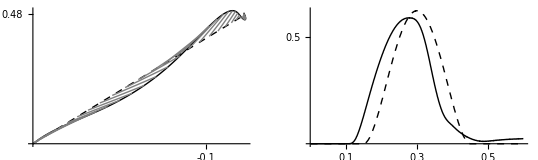

```mathematica
SetTrial[0];

(* Joint trajectories *)
elbAng=NtoD["angleElbow"]/Degree;
elbDes = NtoD["desElbow"]/Degree;
elbCom = NtoD["comElbow"]/Degree;
angleElb =TimePlotD[elbAng,{PlotStyle->{Black}, AxesLabel->{"time","angle"}}];
desAngleElb = TimePlotD[elbDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleElb = TimePlotD[elbCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];

shdAng=NtoD["angleShoulder"]/Degree;
shdDes = NtoD["desShoulder"]/Degree;
shdCom = NtoD["comShoulder"]/Degree;
angleShd= TimePlotD[shdAng,{PlotStyle->{Black}}];
desAngleShd = TimePlotD[shdDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleShd = TimePlotD[shdCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];
elbow = Show[angleElb, desAngleElb, comAngleElb];
shoulder = Show[angleShd, desAngleShd, comAngleShd];

(* Calculate derivatives *)
accScale = 10;

velElb= TimePlot["velocityElbow",{PlotStyle->{Black}, AxesLabel->{"time","velocity"}}];
desVelElbD = Differences[NtoD["desElbow", bestFitDelay]]/dt;
desVelElbD = PadRight[desVelElbD,Length[time],Last[desVelElbD]];
desVelElb = TimePlotD[desVelElbD,{PlotStyle->{Black,Dashed}}];
desAccElbD = Differences[desVelElbD]/dt/accScale;
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElbD = MovingAverage[desAccElbD,3];
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElb = TimePlotD[desAccElbD,{PlotStyle->{Gray}}];

velShd= TimePlot["velocityShoulder",{PlotStyle->{Black}}];
desVelShdD = Differences[NtoD["desShoulder", bestFitDelay]]/dt;
desVelShdD = Append[desVelShdD,desVelShdD[[Length[desVelShdD]]]];
desVelShd = TimePlotD[desVelShdD,{PlotStyle->{Black,Dashed}}];
desAccShdD = Differences[desVelShdD]/dt/accScale;
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShdD = MovingAverage[desAccShdD,3];
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShd = TimePlotD[desAccShdD,{PlotStyle->{Gray}}];

velsElb = Show[velElb, desVelElb, desAccElb];
velsShd = Show[velShd, desVelShd, desAccShd];
vels = Show[velElb,velShd];

(* Forces applied at joints, total is more or less acceleration *)
itElbD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msElbD = NtoD["torqueElbow"];
totalElbD = msElbD +itElbD;
totalElb = TimePlotD[totalElbD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, AxesLabel->{"time","forceElb"}}];
trqElb= TimePlot["torqueElbow",{PlotStyle->Black}];
itElb = TimePlotD[itElbD,{PlotStyle->{Black,Dashed}}];
(*opttotalP = TimePlotOptima[totalElbD, time];
optitP = TimePlotOptima[itElbD, time];
optmsP = TimePlotOptima[msElbD, time];*)
trqsElb = Show[totalElb,trqElb, itElb(*, opttotalP,optitP, optmsP*)];

(*Maxima[totalElbD,time][[1]]*)

itShdD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
totalShdD = NtoD["torqueShoulder"]+itShdD;
totalShd = TimePlotD[totalShdD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},AxesLabel->{"time","forceShd"}}];
trqShd= TimePlot["torqueShoulder",{PlotStyle->Black}];
itShd = TimePlotD[itShdD,{PlotStyle->{Black,Dashed}}];
trqsShd = Show[totalShd,trqShd, itShd];


(* Effector space trajectories, i.e. cartesian position *)
xPos = TimePlot["x",{PlotStyle->{Black}, AxesLabel->{"time","x,y"}}];
desX = TimePlot["desX",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comX = TimePlot["comX",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
yPos = TimePlot["y",{PlotStyle->{Black}}];
desY = TimePlot["desY",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comY = TimePlot["comY",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
pos = Show[xPos,yPos, desX, desY];
posX = Show[xPos, desX, comX];
posY = Show[yPos, desY, comY];

(* XY plot *)
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->Black,AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
startPos = Graphics[{PointSize[Large],Point[First[positions]]}];
desX = Shift[NtoD["desX"],-50];
desY = Shift[NtoD["desY"],-50];
desPos = Transpose[{desX,desY}];
desCartPos = ListLinePlot[desPos,plotOptions,PlotStyle->{Black,Dashed},AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
sample=Table[{positions[[i]],desPos[[i]]},{i,50,Length[desPos],10}];
paral=Graphics[{Gray,Line[sample]}];
xyPos = Show[cartesianPos,desCartPos,paral];

(* Calculate tangential velocity *)
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]];
tangVel=TimePlotD[vels,{PlotStyle->{Black},AxesLabel->{"time","vel"}}];
desVels = Map[Norm,Differences[desPos]]/dt;
desVels = PadRight[desVels,Length[time],Last[desVels]];
tangDesVel = TimePlotD[desVels,{PlotStyle->{Black,Dashed},AxesLabel->{"time","vel"}}];
cartVels = Show[tangVel,tangDesVel]; 

(*(gg=GraphicsGrid[{{pos,angles,vels},{accs,trqsElb, trqsShd}}, ImageSize->{1200}]*)
armPlots=GraphicsGrid[{{xyPos, cartVels},{posX, posY},{elbow, shoulder}, {velsElb,velsShd}, {trqsElb,trqsShd}}, ImageSize->graphicsWidth];

posVelPl = GraphicsRow[{
Show[xyPos,Ticks->{LinTicks[-0.15,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.45,0.53,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}], 
Show[cartVels,Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,2,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}]
},ImageSize->19cm]

(*Export["export.pdf", gg, "pdf"]*)
(*Export[figExpPath<>"Ablation1.eps",posVelPl]*)
```

## Reflex plots

```mathematica
(* Input: desired contraction modified by intersegmental input *)
desContrElbAgP =  TimePlot["reflexElbDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrElbAnP =  TimePlot["reflexElbDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrElbAgP =  TimePlot["reflexElbComContractionAg",{PlotStyle->{Gray}}];
comContrElbAnP =  TimePlot["reflexElbComContractionAn",{PlotStyle->{Gray,Dashed}}];
actContrElbAgP =  TimePlot["reflexElbActContractionAg",{PlotStyle->{LightGray}}];
actContrElbAnP =  TimePlot["reflexElbActContractionAn",{PlotStyle->{LightGray,Dashed}}];
desContrElbPlot =Show[desContrElbAgP,desContrElbAnP,comContrElbAgP,comContrElbAnP,actContrElbAgP,actContrElbAnP];

desContrShdAgP =  TimePlot["reflexShdDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrShdAnP =  TimePlot["reflexShdDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrShdAgP =  TimePlot["reflexShdComContractionAg",{PlotStyle->{Gray}}];
comContrShdAnP =  TimePlot["reflexShdComContractionAn",{PlotStyle->{Gray,Dashed}}];
actContrShdAgP =  TimePlot["reflexShdActContractionAg",{PlotStyle->{LightGray}}];
actContrShdAnP =  TimePlot["reflexShdActContractionAn",{PlotStyle->{LightGray,Dashed}}];
desContrShdPlot =Show[desContrShdAgP,desContrShdAnP,comContrShdAgP,comContrShdAnP,actContrShdAgP,actContrShdAnP];

(* Overall output: alpha MN *)
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ];

aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ];

(* Open loop activation *)
oplpElbAgP =  TimePlot["reflexElbOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpElbAnP =  TimePlot["reflexElbOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpElbPlot=Show[oplpElbAgP,oplpElbAnP ];

oplpShdAgP =  TimePlot["reflexShdOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpShdAnP =  TimePlot["reflexShdOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpShdPlot=Show[oplpShdAgP,oplpShdAnP ];

(* Spindles *)
spElbAgP =  TimePlot["reflexElbSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spElbAnP =  TimePlot["reflexElbSpResAn",{PlotStyle->{Black,Dashed}}];
spindleElbPlot =Show[spElbAgP,spElbAnP ];

spShdAgP =  TimePlot["reflexShdSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spShdAnP =  TimePlot["reflexShdSpResAn",{PlotStyle->{Black,Dashed}}];
spindleShdPlot =Show[spShdAgP,spShdAnP ];

(* Spindles components*)
spElbAgPosP =  TimePlot["reflexElbPosResAg",{PlotStyle->Black, AxesLabel->{"time","spCmpAg"}}];
spElbAgVelP =  TimePlot["reflexElbVelResAg",{PlotStyle->{Black,Dashed}}];
spElbAgDmpP =  TimePlot["reflexElbDmpResAg",{PlotStyle->{Black,Dotted}}];
spShdAgPosP =  TimePlot["reflexShdPosResAg",{PlotStyle->Black}];
spShdAgVelP =  TimePlot["reflexShdVelResAg",{PlotStyle->{Black,Dashed}}];
spShdAgDmpP =  TimePlot["reflexShdDmpResAg",{PlotStyle->{Black,Dotted}}];
spCmpElbAgPlot =Show[spElbAgPosP,spElbAgVelP,spElbAgDmpP];
spCmpShdAgPlot =Show[spShdAgPosP,spShdAgVelP,spShdAgDmpP];

spElbAnPosP =  TimePlot["reflexElbPosResAn",{PlotStyle->Black, AxesLabel->{"time","spCmpAn"}}];
spElbAnVelP =  TimePlot["reflexElbVelResAn",{PlotStyle->{Black,Dashed}}];spElbAnDmpP =  TimePlot["reflexElbDmpResAn",{PlotStyle->{Black,Dotted}}];
spShdAnPosP =  TimePlot["reflexShdPosResAn",{PlotStyle->Black}];
spShdAnVelP =  TimePlot["reflexShdVelResAn",{PlotStyle->{Black,Dashed}}];spShdAnDmpP =  TimePlot["reflexShdDmpResAn",{PlotStyle->{Black,Dotted}}];
spCmpElbAnPlot =Show[spElbAnPosP,spElbAnVelP,spElbAnDmpP];
spCmpShdAnPlot =Show[spShdAnPosP,spShdAnVelP,spShdAnDmpP];

(* IaIn activation *)
iainElbAgP =  TimePlot["reflexElbIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainElbAnP =  TimePlot["reflexElbIaInAn",{PlotStyle->{Black,Dashed}}];
iainElbPlot=Show[iainElbAgP,iainElbAnP ];
iainShdAgP =  TimePlot["reflexShdIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainShdAnP =  TimePlot["reflexShdIaInAn",{PlotStyle->{Black,Dashed}}];
iainShdPlot=Show[iainShdAgP,iainShdAnP ];

(* IbIn activation *)
ibinElbAgP =  TimePlot["reflexElbIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinElbAnP =  TimePlot["reflexElbIbInAn",{PlotStyle->{Black,Dashed}}];
ibinElbPlot=Show[ibinElbAgP,ibinElbAnP ];
ibinShdAgP =  TimePlot["reflexShdIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinShdAnP =  TimePlot["reflexShdIbInAn",{PlotStyle->{Black,Dashed}}];
ibinShdPlot=Show[ibinShdAgP,ibinShdAnP ];

(* Rn activation *)
rnElbAgP =  TimePlot["reflexElbRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnElbAnP =  TimePlot["reflexElbRenshawAn",{PlotStyle->{Black,Dashed}}];
rnElbPlot=Show[rnElbAgP,rnElbAnP ];
rnShdAgP =  TimePlot["reflexShdRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnShdAnP =  TimePlot["reflexShdRenshawAn",{PlotStyle->{Black,Dashed}}];
rnShdPlot=Show[rnShdAgP,rnShdAnP ];

reflexPlots = GraphicsGrid[{{desContrElbPlot, desContrShdPlot},{aMNElbPlot, aMNShdPlot}, {oplpElbPlot,oplpShdPlot},{spindleElbPlot,spindleShdPlot},{spCmpElbAgPlot,spCmpShdAgPlot},{spCmpElbAnPlot,spCmpShdAnPlot},{iainElbPlot,iainShdPlot},{ibinElbPlot,ibinShdPlot},{rnElbPlot, rnShdPlot}}, ImageSize->graphicsWidth];
```

## Muscle Plots

```mathematica
elbAgActP = TimePlot["ElbowFlexorAct",{PlotStyle->{Black},AxesLabel->{"time","Act"}}];
elbAnActP = TimePlot["ElbowExtensorAct", {PlotStyle->{Black,Dashed}}];
elbAct = Show[elbAgActP, elbAnActP];

shdAgActP = TimePlot["ShoulderFlexorAct",{PlotStyle->{Black}}];
shdAnActP = TimePlot["ShoulderExtensorAct", {PlotStyle->{Black,Dashed}}];
shdAct = Show[shdAgActP, shdAnActP];


elbAgFrcP = TimePlot["ElbowFlexorForce",{PlotStyle->{Black},AxesLabel->{"time","Force"}}];
elbAnFrcP = TimePlot["ElbowExtensorForce", {PlotStyle->{Black,Dashed}}];
elbFrcTotal = Show[elbAgFrcP, elbAnFrcP];

shdAgFrcP = TimePlot["ShoulderFlexorForce",{PlotStyle->{Black}}];
shdAnFrcP = TimePlot["ShoulderExtensorForce", {PlotStyle->{Black,Dashed}}];
shdFrcTotal = Show[shdAgFrcP, shdAnFrcP];


elbAgLengthP = TimePlot["ElbowFlexorLengthNorm",{PlotStyle->{Black},AxesLabel->{"time","Length"}}];
elbAnLengthP = TimePlot["ElbowExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
elbAgVelP = TimePlot["ElbowFlexorVelocityNorm",{PlotStyle->{Gray}}];
elbAnVelP = TimePlot["ElbowExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
elbKin = Show[elbAgLengthP,elbAnLengthP(*,elbAgVelP,elbAnVelP*)];

shdAgLengthP = TimePlot["ShoulderFlexorLengthNorm",{PlotStyle->{Black}}];
shdAnLengthP = TimePlot["ShoulderExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
shdAgVelP = TimePlot["ShoulderFlexorVelocityNorm",{PlotStyle->{Gray}}];
shdAnVelP = TimePlot["ShoulderExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
shdKin = Show[shdAgLengthP,shdAnLengthP(*,shdAgVelP,shdAnVelP*)];

elbAgActFrcP = TimePlot["ElbowFlexorFrcAct", {PlotStyle->{Black},AxesLabel->{"time","FrcCmp"}}];
elbAnActFrcP = TimePlot["ElbowExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
elbAgVelFrcP = TimePlot["ElbowFlexorFrcVel", {PlotStyle->{Gray},AxesLabel->{"time","FrcCmp"}}];
elbAnVelFrcP = TimePlot["ElbowExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
elbAgPsvFrcP = TimePlot["ElbowFlexorFrcPsv", {PlotStyle->{LightGray},AxesLabel->{"time","FrcCmp"}}];
elbAnPsvFrcP = TimePlot["ElbowExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
elbFrc = Show[elbAgActFrcP, elbAnActFrcP,elbAgVelFrcP,elbAnVelFrcP(*,elbAgPsvFrcP,elbAnPsvFrcP*)];

shdAgActFrcP = TimePlot["ShoulderFlexorFrcAct", {PlotStyle->{Black}}];
shdAnActFrcP = TimePlot["ShoulderExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
shdAgVelFrcP = TimePlot["ShoulderFlexorFrcVel", {PlotStyle->{Gray}}];
shdAnVelFrcP = TimePlot["ShoulderExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
shdAgPsvFrcP = TimePlot["ShoulderFlexorFrcPsv", {PlotStyle->{LightGray}}];
shdAnPsvFrcP = TimePlot["ShoulderExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
shdFrc = Show[shdAgActFrcP, shdAnActFrcP,shdAgVelFrcP,shdAnVelFrcP(*,shdAgPsvFrcP,shdAnPsvFrcP*)];


shdNetTrq = NtoD["ShoulderFlexorTorque", bestFitDelay] - NtoD["ShoulderExtensorTorque"];
elbNetTrq = NtoD["ElbowFlexorTorque", bestFitDelay] - NtoD["ElbowExtensorTorque"];
elbNetTrqP = TimePlotD[elbNetTrq,{}];
shdNetTrqP = TimePlotD[shdNetTrq,{}];

elbAgMaP = TimePlot["ElbowFlexorMomentArm",{PlotStyle->{Black},AxesLabel->{"time","MA"}}];
elbAnMaP = TimePlot["ElbowExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
elbAgTorqueP = TimePlot["ElbowFlexorTorque",{PlotStyle->{Black},AxesLabel->{"time","Torque"}}];
elbAnTorqueP = TimePlot["ElbowExtensorTorque", {PlotStyle->{Black,Dashed}}];
elbTrq = Show[elbAgTorqueP,elbAnTorqueP, elbNetTrqP];
elbMa = Show[elbAgMaP, elbAnMaP];

shdAgMaP = TimePlot["ShoulderFlexorMomentArm",{PlotStyle->{Black}}];
shdAnMaP = TimePlot["ShoulderExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
shdAgTorqueP = TimePlot["ShoulderFlexorTorque",{PlotStyle->{Black}}];
shdAnTorqueP = TimePlot["ShoulderExtensorTorque", {PlotStyle->{Black,Dashed}}];
shdTrq = Show[shdAgTorqueP,shdAnTorqueP, shdNetTrqP];
shdMa = Show[shdAgMaP, shdAnMaP];

musclePlots = GraphicsGrid[{{elbAct,shdAct},{elbFrcTotal,shdFrcTotal},{elbKin,shdKin},{elbFrc,shdFrc},{elbMa,shdMa},{elbTrq,shdTrq}},ImageSize->graphicsWidth];
```

## Phase Space plots

```mathematica
angleElbD = NtoD["angleElbow"];
velElbD = NtoD["velocityElbow"];
desAngleElbD = NtoD["desElbow",bestFitDelay];
actElbPhase = ListLinePlot[Transpose[{angleElbD,velElbD}],PlotStyle->Black,AxesLabel->{"angle","vel"},plotOptions];
desElbPhase = ListLinePlot[Transpose[{desAngleElbD,desVelElbD}],PlotStyle->{Black,Dashed},plotOptions];
elbPhase = Show[actElbPhase,desElbPhase];

angleShdD = NtoD["angleShoulder"];
velShdD = NtoD["velocityShoulder"];
desAngleShdD = NtoD["desShoulder",bestFitDelay];
actShdPhase = ListLinePlot[Transpose[{angleShdD,velShdD}],PlotStyle->Black,AxesLabel->{"angle","vel"}, plotOptions];
desShdPhase = ListLinePlot[Transpose[{desAngleShdD,desVelShdD}], PlotStyle->{Black,Dashed},plotOptions];
shdPhase = Show[actShdPhase, desShdPhase];

phSpacePlots =GraphicsRow[{elbPhase, shdPhase}, ImageSize->graphicsWidth];
```

## Output

Arm States

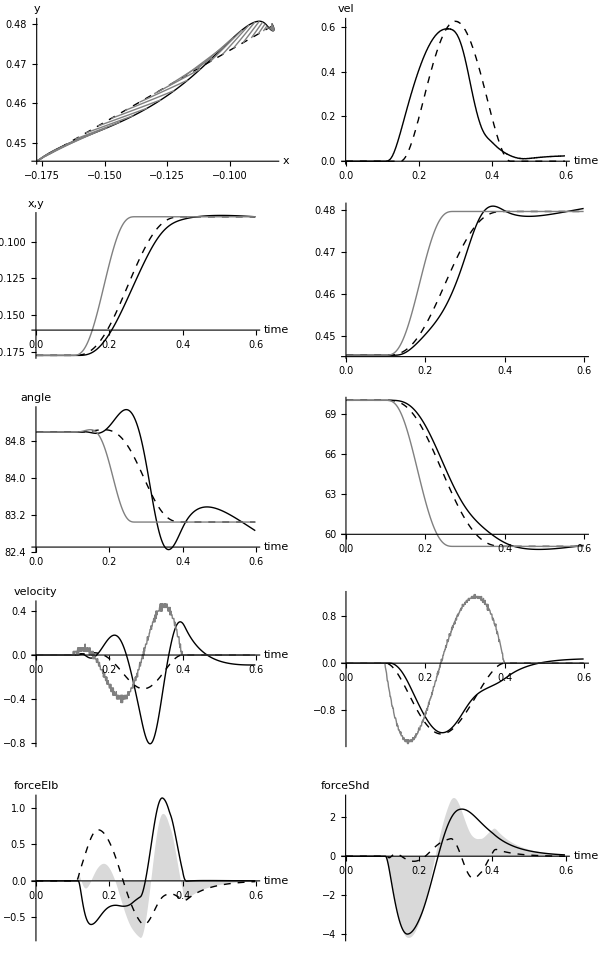

Reflex States

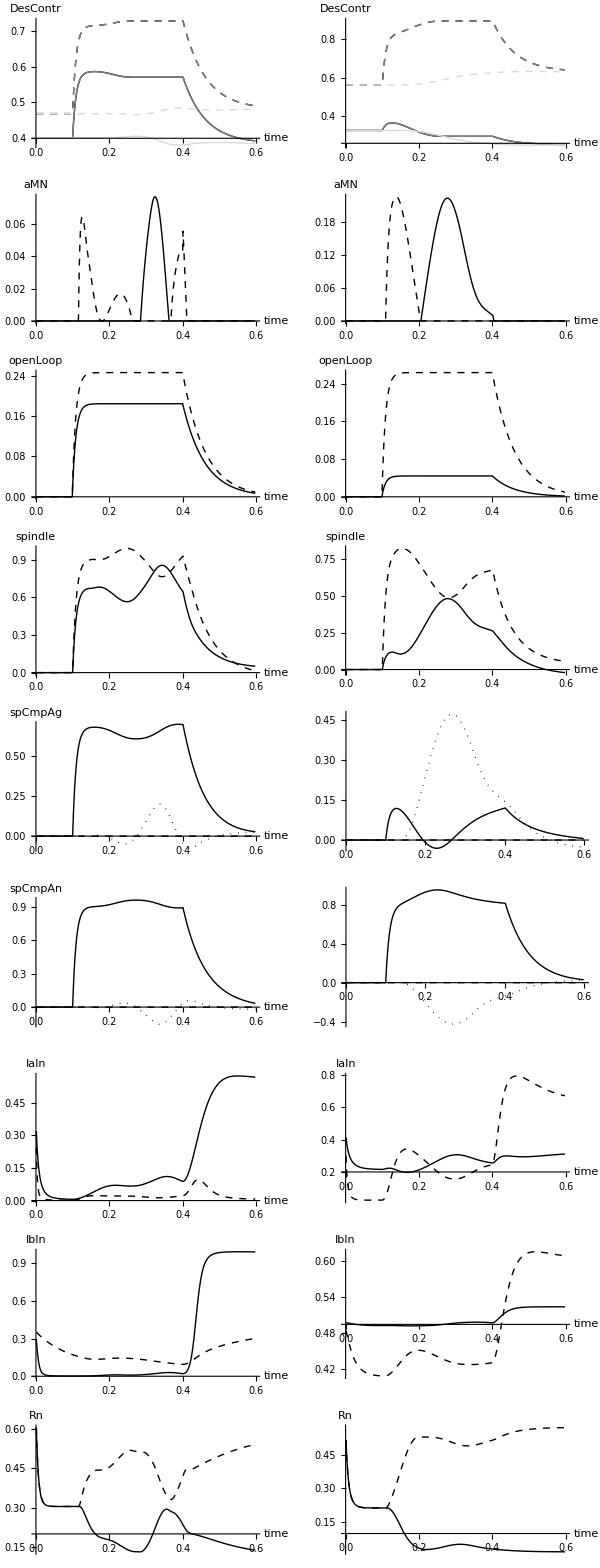

Muscle States

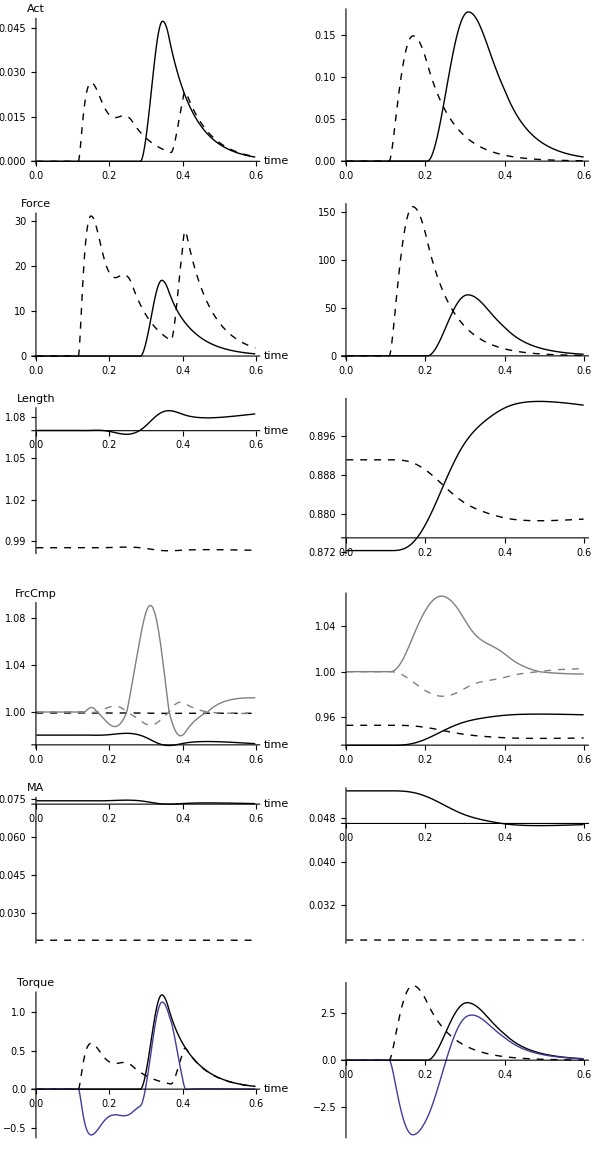

Phase space

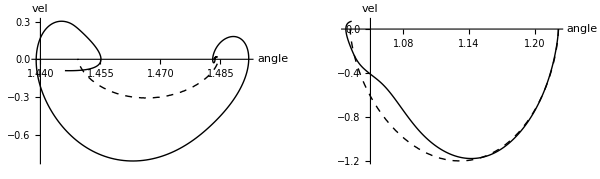

```mathematica
Print[Style["Arm States","Subtitle"]]
armPlots

Print[Style["Reflex States","Subtitle"]]
reflexPlots

Print[Style["Muscle States","Subtitle"]]
musclePlots

Print[Style["Phase space","Subtitle"]]
phSpacePlots
```

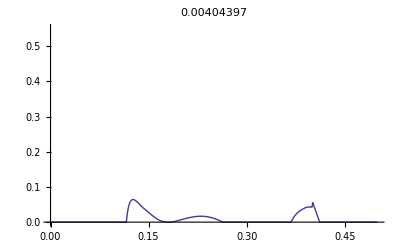

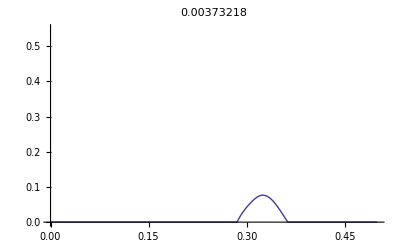

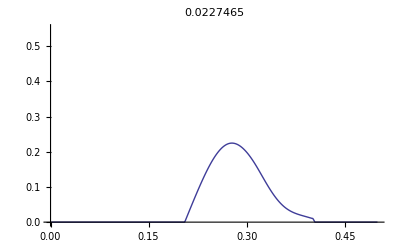

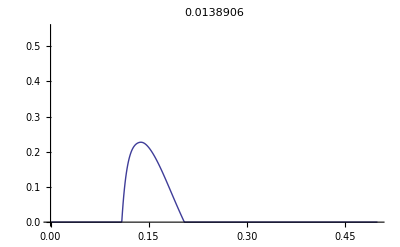

```mathematica
SetTrial[0];

ImpArea[tr_,var_,fr_,to_]:=Module[{},
SetTrial[tr];
s=NtoD[var];
s=s[[fr;;to]];
l=Length[s];
t = 0.001*Range[1,l];
d=ConstantArray[0.001,l];
ListLinePlot[Transpose[{t,s}],PlotRange->{Automatic,{0,0.55}},PlotLabel->Dot[d,s]]
];

ImpArea[0,"reflexElbMNAn",1,500]
ImpArea[0,"reflexElbMNAg",1,500]
ImpArea[0,"reflexShdMNAg",1,500]
ImpArea[0,"reflexShdMNAn",1,500]
```